Inversion W[x0]

```mathematica
Clear[λ0,τ,τR,β,δλ,x,W,x0]

ΔF = δλ/(2β λ0)-δλ^2/(4β λ0^2);


ΔF = x^2/2 δλ-(β(x^4/4-x^2/(4β λ0)))δλ^2/2;

g[y_]=y/τ;

W[x_]=Expand[ΔF+δλ^2/2 Assuming[τ>0, Integrate[(β(x^4/4-x^2/(4β λ0)))Exp[(-Abs[u-v])/τR]D[g[u],u]D[g[v],v],{u,0,τ},{v,0,τ}]]];

solve1=Solve[W[z]==y,z];

x0[y_,τ_]=z/.solve1[[4]];

f0[w_,t_]=Abs[D[x0[w,t],w]];
```

Writing ρ(x0(W))*dx0/dW

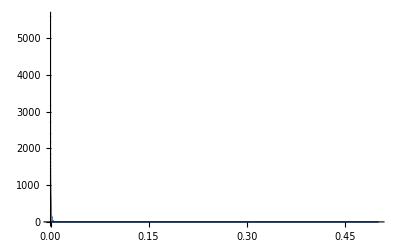

```mathematica
Clear[λ0,τR,τ,δλ,β,x,w]

λ0=1;
δλ=0.001;
τR=1;
τ=1;
β=1;

ΔF=N[-Log[(β λ0)^(1/2)/(β (δλ+λ0))^(1/2)]/β];

ρ0[x_]=Exp[-β/2 λ0 x^2]/(2π/ (β λ0))^(1/2);

listaw=Table[{w,Abs[2f0[w,τ]]ρ0[x0[w,τ]]},{w,0.00001,0.5,0.00001}];

ListPlot[listaw,PlotRange->{{0,0.5},Full}]

Clear[λ0,γ,τR,τ,δλ,β]
```

Initial parameters and important functions

```mathematica
Clear[λ0,γ,τR,τ,δλ,β,x0]

β=1;
γ=2;
λ0=1;
δλ=5;
τR = γ/(2λ0);
τ=0.1;

Nprocess=10000;

ρ0[y_]=Exp[-β/2 λ0 y^2]/(2π/ (β λ0))^(1/2);

ΔF=N[-Log[(β λ0)^(1/2)/(β (δλ+λ0))^(1/2)]/β];

dataWN=List[];
dataWLR=List[];
dataExpWN=List[];
dataExpWLR=List[];
(*dataCompLR=List[];
dataCompLR2=List[];*)

W[x0_]=Simplify[Abs[1/(4 β √(δλ λ0^3 τ τR^3))((√(2/π δλ/λ0 τ/τR)Exp[-λ0/(2 δλ)τ/τR](1+τ/(2τR)δλ/λ0)) (ⅇ^((λ0 τ)/(2 δλ τR)) √(2 π) x0^2 β δλ λ0^2 τR^2-π √(δλ λ0^3 τ τR^3) Erfi[(√((λ0 τ)/(δλ τR)))/(√2)])-√((λ0^5 τ^3 τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-(λ0 τ)/(2 δλ τR)]+(δλ+λ0)^2 τ √((λ0 τ τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-((δλ+λ0)^2 τ)/(2 δλ λ0 τR)])]];

W[x0_]=1/(4 β √(δλ λ0^3 τ τR^3))((-Erf[(√((λ0 τ)/(δλ τR)))/(√2)]+Erf[(δλ+λ0)/(√2 √((δλ λ0 τR)/τ))]) (ⅇ^((λ0 τ)/(2 δλ τR)) √(2 π) x0^2 β δλ λ0^2 τR^2-π √(δλ λ0^3 τ τR^3) Erfi[(√((λ0 τ)/(δλ τR)))/(√2)])-√((λ0^5 τ^3 τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-(λ0 τ)/(2 δλ τR)]+(δλ+λ0)^2 τ √((λ0 τ τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-((δλ+λ0)^2 τ)/(2 δλ λ0 τR)])
```

0.353553 (0.439368+0.491393 (-0.251501+12.6591 x0^2))

Numeric histogram

0.930854

{{0.001,0.00698626},{0.005,0.010012},{0.01,0.0292236},{0.05,0.0020936},{0.1,0.00509387},{0.5,0.0566453},{1,0.0678284},{1,0.00325492},{0.5,0.0107678},{5,0.0286463}}

{{0.001,0.0382203},{0.005,0.0257803},{0.01,0.0286696},{0.05,0.0207609},{0.1,0.00509032},{0.5,0.0873459},{1,0.0469817},{1,0.0869178},{0.5,0.0438785},{5,0.179001}}

9.92879

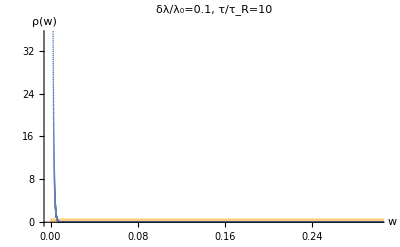

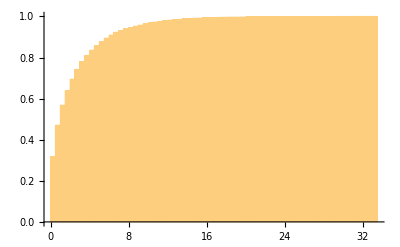

```mathematica
Do[

x0=RandomVariate[ProbabilityDistribution[ρ0[y],{y,-Infinity,Infinity}]];

dataWN=AppendTo[dataWN,W[x0]];
dataExpWN=AppendTo[dataExpWN,Exp[-β(W[x0]-ΔF)]];

,{n,1,Nprocess}];

Mean[dataExpWN]

(*dataCompLR=AppendTo[dataCompLR,{Mean[dataWN]/(ΔF+β/2 Variance[dataWN]),δλ/λ0}]*)

dataCompLR=AppendTo[dataCompLR,{δλ/λ0,Abs[(Mean[dataWN]-(δλ/(2 β λ0)-(3 δλ^2)/(8 β λ0^2) +δλ^2/(8 β λ0^2)+(3 δλ^2 τR)/(4 τ β λ0^2)-(δλ^2 τR)/(4 β λ0^2 τ)-(3 δλ^2 τR^2)/(4 β λ0^2 τ^2)+(ⅇ^(-τ/τR) 3 δλ^2 τR^2)/(4 β λ0^2 τ^2)+(δλ^2 τR^2)/(4 β λ0^2 τ^2)-(ⅇ^(-τ/τR)  δλ^2 τR^2)/(4 β λ0^2 τ^2)))/(δλ/(2 β λ0)-(3 δλ^2)/(8 β λ0^2) +δλ^2/(8 β λ0^2)+(3 δλ^2 τR)/(4 τ β λ0^2)-(δλ^2 τR)/(4 β λ0^2 τ)-(3 δλ^2 τR^2)/(4 β λ0^2 τ^2)+(ⅇ^(-τ/τR) 3 δλ^2 τR^2)/(4 β λ0^2 τ^2)+(δλ^2 τR^2)/(4 β λ0^2 τ^2)-(ⅇ^(-τ/τR)  δλ^2 τR^2)/(4 β λ0^2 τ^2))]}]

dataCompLR2=AppendTo[dataCompLR2,{δλ/λ0,Abs[(Variance[dataWN]-((2/β)((3 δλ^2 τR)/(4 τ β λ0^2)-(δλ^2 τR)/(4 β λ0^2 τ)-(3 δλ^2 τR^2)/(4 β λ0^2 τ^2)+(ⅇ^(-τ/τR) 3 δλ^2 τR^2)/(4 β λ0^2 τ^2)+(δλ^2 τR^2)/(4 β λ0^2 τ^2)-(ⅇ^(-τ/τR)  δλ^2 τR^2)/(4 β λ0^2 τ^2))))/((2/β)((3 δλ^2 τR)/(4 τ β λ0^2)-(δλ^2 τR)/(4 β λ0^2 τ)-(3 δλ^2 τR^2)/(4 β λ0^2 τ^2)+(ⅇ^(-τ/τR) 3 δλ^2 τR^2)/(4 β λ0^2 τ^2)+(δλ^2 τR^2)/(4 β λ0^2 τ^2)-(ⅇ^(-τ/τR)  δλ^2 τR^2)/(4 β λ0^2 τ^2)))]}]

(*FindDistribution[dataWN]

DistributionFitTest[dataWN,FindDistribution[dataWN]]*)

Variance[dataWN]

g1=Histogram[dataWN,Automatic,"PDF",PlotRange->{{0,0.3},{0,35}}];

g2=ListPlot[listaw,PlotRange->Full];

Show[{g1,g2},AxesLabel->{"w","ρ(w)"},PlotLabel->"δλ/λ_0=0.1, τ/τ_R=10"]

Histogram[dataWN,Automatic,"CDF",PlotRange->Full]
```

Error analysis

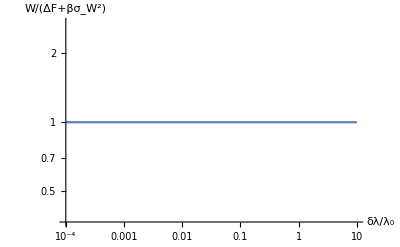

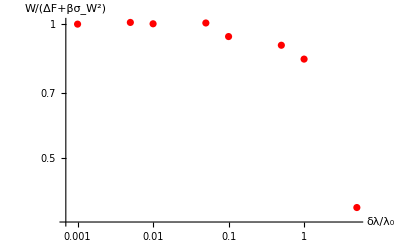

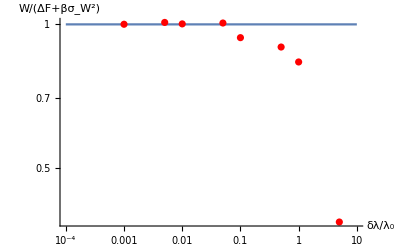

```mathematica
lista={{0.01,1.0023165868249073},{0.05,1.0065559374341098},{0.1,0.938061870974432},{0.5,0.8966495067015605},{1,0.8344073201603287},{0.005,1.0093776124294052},{0.001,1.0005616385358354},{5,0.3861146817272218}};

g1 = LogLogPlot[1,{x,0.0001,10},AxesLabel->{"δλ/λ_0","W/(ΔF+βσ_W^2)"},PlotRange->Full];

g2=ListLogLogPlot[lista,AxesLabel->{"δλ/λ_0","W/(ΔF+βσ_W^2)"},PlotRange->Full,PlotStyle->{Red}];

Show[{g1,g2}]
```

```mathematica
{{1.0023165868249073,0.01},{1.0065559374341098,0.05},{0.938061870974432,0.1},{0.8966495067015605,0.5},{0.8344073201603287,1},{1.0093776124294052,0.005},{1.0005616385358354,0.001},{0.3861146817272218,5}}
```

Moment analysis

```mathematica
Clear[λ0,γ,τR,τ,δλ,β,x0]

β=1;
γ=2;
λ0=1;
δλ=0.5;
τR = γ/(2λ0);
τ=1;

Nprocess=10000;

ρ0[y_]=Exp[-β/2 λ0 y^2]/(2π/ (β λ0))^(1/2);

ΔF=N[-Log[(β λ0)^(1/2)/(β (δλ+λ0))^(1/2)]/β];

dataWN=List[];
dataWLR=List[];
dataExpWN=List[];
dataExpWLR=List[];
(*dataCompLR=List[];
dataCompLR2=List[];*)

(* Second-order approximation to avoid error for small δλ/λ0 *)

W[x0_]=Simplify[Abs[1/(4 β √(δλ λ0^3 τ τR^3))((√(2/π δλ/λ0 τ/τR)Exp[-λ0/(2 δλ)τ/τR](1+τ/(2τR)δλ/λ0)) (ⅇ^((λ0 τ)/(2 δλ τR)) √(2 π) x0^2 β δλ λ0^2 τR^2-π √(δλ λ0^3 τ τR^3) Erfi[(√((λ0 τ)/(δλ τR)))/(√2)])-√((λ0^5 τ^3 τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-(λ0 τ)/(2 δλ τR)]+(δλ+λ0)^2 τ √((λ0 τ τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-((δλ+λ0)^2 τ)/(2 δλ λ0 τR)])]];

(* Exact work  *)

(*W[x0_]=1/(4 β √(δλ λ0^3 τ τR^3))((-Erf[(√((λ0 τ)/(δλ τR)))/(√2)]+Erf[(δλ+λ0)/(√2 √((δλ λ0 τR)/τ))]) (ⅇ^((λ0 τ)/(2 δλ τR)) √(2 π) x0^2 β δλ λ0^2 τR^2-π √(δλ λ0^3 τ τR^3) Erfi[(√((λ0 τ)/(δλ τR)))/(√2)])-√((λ0^5 τ^3 τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-(λ0 τ)/(2 δλ τR)]+(δλ+λ0)^2 τ √((λ0 τ τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-((δλ+λ0)^2 τ)/(2 δλ λ0 τR)])*)
```

```mathematica
Do[

x0=RandomVariate[ProbabilityDistribution[ρ0[y],{y,-Infinity,Infinity}]];

dataWN=AppendTo[dataWN,W[x0]];
dataWLR=AppendTo[dataWLR,(x0^2 δλ)/2-1/8 x0^4 β δλ^2+(x0^2 δλ^2)/(8 λ0)+(x0^4 β δλ^2 τR)/(4 τ)-(x0^2 δλ^2 τR)/(4 λ0 τ)-(x0^4 β δλ^2 τR^2)/(4 τ^2)+(ⅇ^(-τ/τR) x0^4 β δλ^2 τR^2)/(4 τ^2)+(x0^2 δλ^2 τR^2)/(4 λ0 τ^2)-(ⅇ^(-τ/τR) x0^2 δλ^2 τR^2)/(4 λ0 τ^2)];

dataExpWN=AppendTo[dataExpWN,Exp[-β(W[x0]-ΔF)]];

,{n,1,Nprocess}];

Mean[dataExpWN]

dataCompLR=AppendTo[dataCompLR,{δλ/λ0,Abs[(Mean[dataWN]-Mean[dataWLR])/Mean[dataWN]]}]

dataCompLR2=AppendTo[dataCompLR2,{δλ/λ0,Abs[(Variance[dataWN]-Variance[dataWLR])/Variance[dataWN]]}]
```

0.98998

{{0.001,0.000330722},{0.005,0.00152829},{0.01,0.00262131},{0.05,0.0114327},{0.1,0.000411981},{0.5,0.000710246},{1,0.0144341},{0.1,0.0202959},{1,0.353385},{5,0.89511},{0.5,0.141243}}

{{0.001,0.00164133},{0.005,0.00827017},{0.01,0.0158017},{0.05,0.0644337},{0.1,1.40272},{0.5,0.992383},{1,0.683823},{0.1,0.11106},{1,0.771583},{5,0.844075},{0.5,0.470664}}

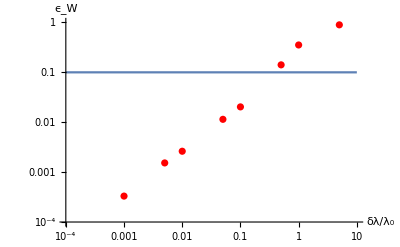

```mathematica
listaMean={{0.001,0.0003307219533104406},{0.005,0.0015282906081531286},{0.01,0.002621313494936097},{0.05,0.01143270084672248},{0.1,0.020295862547526484},{1,0.3533846283181283},{5,0.8951103754639395},{0.5,0.14124322427824165}};

g1 = LogLogPlot[0.1,{x,0.0001,10},AxesLabel->{"δλ/λ_0","ϵ_W"},PlotRange->{{0.0001,10},{0.0001,1}}];

g2=ListLogLogPlot[listaMean,AxesLabel->{"δλ/λ_0","ϵ_W"},PlotRange->{{0.0001,10},{0.001,1}},PlotStyle->{Red}];

Show[{g1,g2}]
```

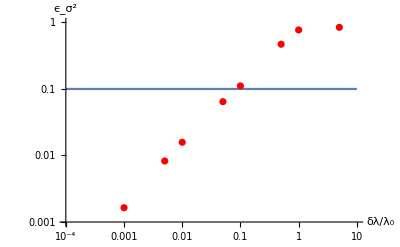

```mathematica
listaVar={{0.001,0.001641330082470174},{0.005,0.008270168680717406},{0.01,0.015801704351279738},{0.05,0.06443367992364317},{0.1,0.1110599069022353},{1,0.7715825634322064},{5,0.844074791349023},{0.5,0.4706637925610657}};

g1 = LogLogPlot[0.1,{x,0.0001,10},AxesLabel->{"δλ/λ_0","ϵ_(σ^2)"},PlotRange->{{0.0001,10},{0.001,1}}];

g2=ListLogLogPlot[listaVar,AxesLabel->{"δλ/λ_0","ϵ_(σ^2)"},PlotRange->{{0.0001,10},{0.001,1}},PlotStyle->{Red}];

Show[{g1,g2}]
```

```mathematica
f
```

Linear response histogram

0.926225

1.0092

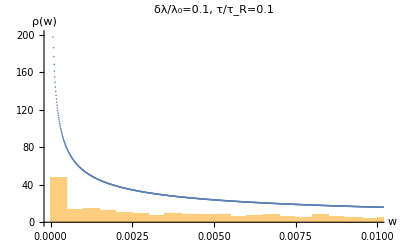

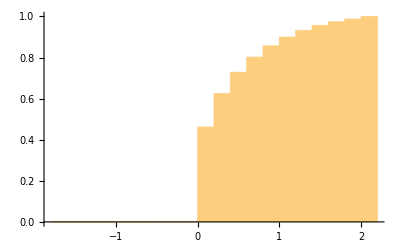

```mathematica
Do[

x=RandomVariate[ProbabilityDistribution[ρ0[y],{y,-Infinity,Infinity}]];
W=(x^2 δλ)/2-1/8 x^4 β δλ^2+(x^2 δλ^2)/(8 λ0)+(x^4 β δλ^2 τR)/(4 τ)-(x^2 δλ^2 τR)/(4 λ0 τ)-(x^4 β δλ^2 τR^2)/(4 τ^2)+(ⅇ^(-τ/τR) x^4 β δλ^2 τR^2)/(4 τ^2)+(x^2 δλ^2 τR^2)/(4 λ0 τ^2)-(ⅇ^(-τ/τR) x^2 δλ^2 τR^2)/(4 λ0 τ^2);

dataWLR=AppendTo[dataWLR,W];
dataExpWLR=AppendTo[dataExpWLR,Exp[-β(W-ΔF)]];

,{k,1,Nprocess}];

Mean[dataWLR]/(ΔF+β/2 Variance[dataWLR])

Mean[dataExpWLR]

g1=Histogram[dataWLR,{0.0005},"PDF",PlotRange->{{0,0.01},{0,200}}];

g2=ListPlot[listaw];

Show[{g1,g2},AxesLabel->{"w","ρ(w)"},PlotLabel->"δλ/λ_0=0.1, τ/τ_R=0.1"]

Histogram[dataWLR,Automatic,"CDF",PlotRange->Full]
```

Calculation of exact W

```mathematica
Clear[λ0,δλ,τ,β,γ,τR]
DSolve[{D[y[t],t]+(λ0+t δλ/τ)/(τR λ0)y[t]-1/(β τR λ0)==0,y[0]==y0},y[t],t]
```

{{y[t]→(ⅇ^(-t/τR-(t^2 δλ)/(2 λ0 τ τR)-(λ0 τ)/(2 δλ τR)) (2 ⅇ^((λ0 τ)/(2 δλ τR)) y0 β √δλ √λ0 √τR-√(2 π) √τ Erfi[(√λ0 √τ)/(√2 √δλ √τR)]+√(2 π) √τ Erfi[(t δλ+λ0 τ)/(√2 √δλ √λ0 √τ √τR)]))/(2 β √δλ √λ0 √τR)}}

```mathematica
Assuming[{δλ>0,λ0>0,τR>0,τ>0,β>0},Integrate[δλ/(4 β √δλ √λ0 √τR τ)ⅇ^(-t/τR-(t^2 δλ)/(2 λ0 τ τR)-(λ0 τ)/(2 δλ τR)) (2 ⅇ^((λ0 τ)/(2 δλ τR)) y0 β √δλ √λ0 √τR-√(2 π) √τ Erfi[(√λ0 √τ)/(√2 √δλ √τR)]+√(2 π) √τ Erfi[(t δλ+λ0 τ)/(√2 √δλ √λ0 √τ √τR)]),{t,0,τ}]]
```

1/(4 β √(δλ λ0^3 τ τR^3))((-Erf[(√((λ0 τ)/(δλ τR)))/(√2)]+Erf[(δλ+λ0)/(√2 √((δλ λ0 τR)/τ))]) (ⅇ^((λ0 τ)/(2 δλ τR)) √(2 π) y0 β δλ λ0^2 τR^2-π √(δλ λ0^3 τ τR^3) Erfi[(√((λ0 τ)/(δλ τR)))/(√2)])-√((λ0^5 τ^3 τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-(λ0 τ)/(2 δλ τR)]+(δλ+λ0)^2 τ √((λ0 τ τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-((δλ+λ0)^2 τ)/(2 δλ λ0 τR)])

```mathematica
W=1/(4 β √(δλ λ0^3 τ τR^3))((-Erf[(√((λ0 τ)/(δλ τR)))/(√2)]+Erf[(δλ+λ0)/(√2 √((δλ λ0 τR)/τ))]) (ⅇ^((λ0 τ)/(2 δλ τR)) √(2 π) x0^2 β δλ λ0^2 τR^2-π √(δλ λ0^3 τ τR^3) Erfi[(√((λ0 τ)/(δλ τR)))/(√2)])-√((λ0^5 τ^3 τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-(λ0 τ)/(2 δλ τR)]+(δλ+λ0)^2 τ √((λ0 τ τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-((δλ+λ0)^2 τ)/(2 δλ λ0 τR)]);

W=1/(4 β √(δλ λ0^3 τ τR^3))((√(2/π δλ/λ0 τ/τR)Exp[-λ0/(2 δλ)τ/τR]) (ⅇ^((λ0 τ)/(2 δλ τR)) √(2 π) x0^2 β δλ λ0^2 τR^2-π √(δλ λ0^3 τ τR^3) Erfi[(√((λ0 τ)/(δλ τR)))/(√2)])-√((λ0^5 τ^3 τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-(λ0 τ)/(2 δλ τR)]+(δλ+λ0)^2 τ √((λ0 τ τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-((δλ+λ0)^2 τ)/(2 δλ λ0 τR)]);
```